```mathematica
ClearAll["Global`*"]
```

```mathematica
Sol=Solve[{rh*H*(1-(H+ahm*M)/kh)==0,rm*M*(1-(M+amh*H)/km)==0},{H,M}]
```

{{H→0,M→km},{H→-(kh-ahm km)/(-1+ahm amh),M→-(-amh kh+km)/(-1+ahm amh)},{H→0,M→0},{H→kh,M→0}}

D-differentiation... soma will influence the germ line... germ cells will incorporate aspects of the soma.

World Population from 1800 to now

WolframAlphaQueryResults

```mathematica
TS=WolframAlpha["World Population from 1800 to now",{{"SensiblePlot:Population:CountryData",1},"FormattedData"}];
data=Delete[TS[[1]][[1,All,2]],1];
data = Delete[data,Table[{i},{i,1,16}]];
```

```mathematica
Export["/Users/justinyeakel/Dropbox/PostDoc/2016_Frankenstein/math/data.dat",data];
```

```mathematica
data = Flatten[Import["/Users/justinyeakel/Dropbox/PostDoc/2016_Frankenstein/math/data.dat"],1];
```

```mathematica
data
```

{1.01519,1.0196,1.02402,1.02844,1.03289,1.04042,1.04807,1.0558,1.06374,1.07172,1.07951,1.08731,1.09519,1.1042,1.11332,1.11825,1.12308,1.12788,1.1326,1.13819,1.14377,1.14934,1.15527,1.16113,1.16706,1.17234,1.17772,1.1831,1.18859,1.19418,1.1997,1.20545,1.21081,1.21642,1.22222,1.22314,1.22437,1.22707,1.22982,1.23252,1.23535,1.23889,1.24213,1.24594,1.24982,1.25442,1.25782,1.26252,1.26664,1.27096,1.27507,1.27936,1.28415,1.28973,1.29454,1.3041,1.31308,1.3224,1.332,1.34305,1.35174,1.36299,1.37291,1.38232,1.39238,1.4033,1.41357,1.42435,1.43523,1.44633,1.45656,1.46719,1.4779,1.48891,1.50015,1.51123,1.52259,1.5343,1.54651,1.55859,1.56995,1.58305,1.59565,1.60838,1.62213,1.63426,1.64836,1.65931,1.66993,1.68118,1.69166,1.70325,1.71541,1.72705,1.73973,1.75433,1.76818,1.78183,1.7948,1.80717,1.81933,1.83066,1.83914,1.8462,1.863,1.8777,1.8955,1.91341,1.93141,1.94955,1.96526,1.9823,2.0022,2.02117,2.04218,2.06252,2.08547,2.10693,2.12708,2.14843,2.16973,2.19175,2.21398,2.23624,2.25517,2.2733,2.29303,2.31105,2.33046,2.35258,2.37847,2.40986,2.44143,2.47313,2.51679,2.55959,2.60516,2.65191,2.70184,2.75663,2.80276,2.85836,2.91433,2.9725,3.03284,3.09419,3.16074,3.22435,3.28876,3.35431,3.41662,3.48201,3.54795,3.61517,3.69619,3.77205,3.84832,3.92467,4.00076,4.07642,4.15141,4.22586,4.3004,4.3759,4.45301,4.5318,4.61212,4.6941,4.77783,4.86329,4.95059,5.03948,5.12911,5.21837,5.30643,5.39294,5.47801,5.56174,5.64442,5.72624,5.80721,5.88726,5.96646,6.04493,6.12277,6.2,6.27672,6.3532,6.42976,6.50665,6.58396,6.66164,6.73961,6.81774,6.89589,6.97404,7.05214}

```mathematica
diffdata = Differences[data];
```

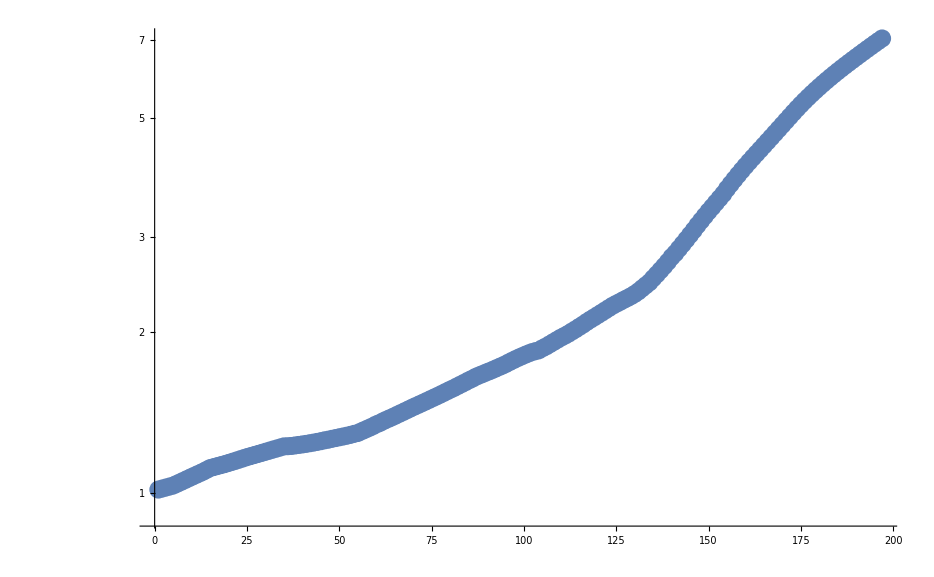

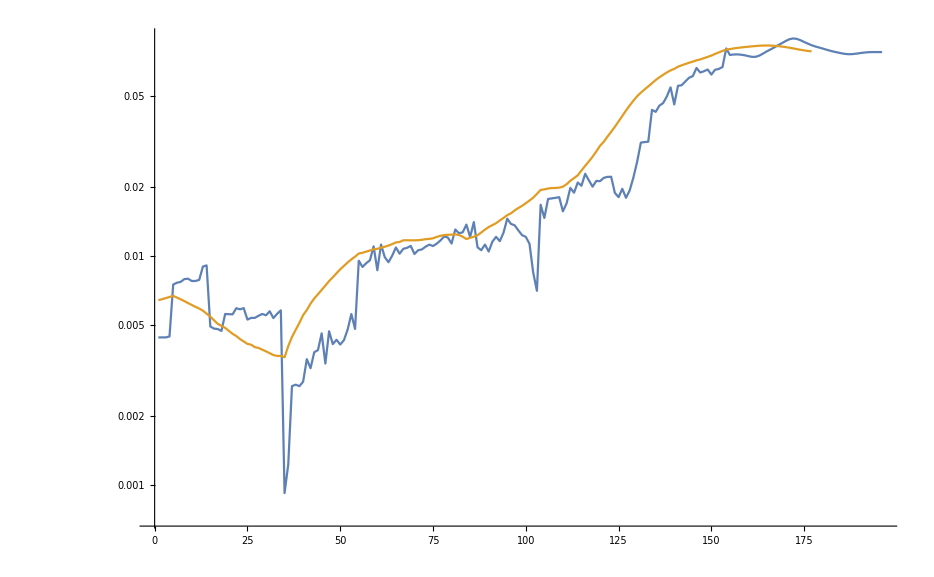

0.00722552

```mathematica
ListLogPlot[data]
ListLogPlot[{diffdata,MovingAverage[diffdata,20]},Joined->True]
Mean[diffdata[[1;;84]]]
```

```mathematica
data[[1]]
```

1.01519

The world without monsters...
Humans start at 1.02x10^9 people in 1816 and end with 7.18x10^9 people today
In our model, the growth rate needs to be at 0.008-0.01 or so to achieve this...

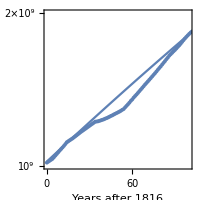

```mathematica
CompDyn[rh_,ahm_,kh_,rm_,amh_,km_,T_] :=

NDSolve[{
H'[t] ==rh*H[t]*(1-(H[t]+ahm*M[t])/kh),
M'[t] ==rm*M[t]*(1-(M[t]+amh*H[t])/km),
H[0]==1.02*10^9,M[0]==0},{H,M},{t,0,T},MaxSteps->Infinity,InterpolationOrder->All];

With[{rh=0.0067,rm=0.01,ahm=5,amh=0.1,kh=10*10^9,km=10*10^6,T=200},
Traj=Evaluate[{H[t],M[t]}/.CompDyn[rh,ahm,kh,rm,amh,km,T] ];
Show[{
LogPlot[Traj,{t,0,T/2},PlotRange->{1*10^9,2*10^9},AspectRatio->1,Frame->True,FrameLabel->{"Years after 1816","Human population"}],
ListLogPlot[Transpose[{Table[i,{i,0,Length[data]-1}],data*10^9}],Joined->False,PlotStyle->Dashed]
},ImageSize->200]
]
```

Dynamics with monster population

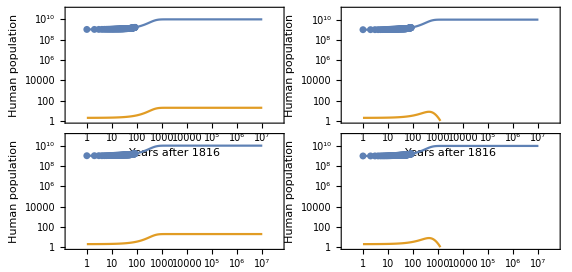

```mathematica
CompDyn[rh_,rm_,ahm_,c_,k_,T_] :=

NDSolve[{
H'[t] ==rh*H[t]*(1-(H[t]+ahm*M[t])/k),
M'[t] ==rm*M[t]*(1-(M[t]+ahm/c*H[t])/k),
H[1]==1.02*10^9,M[1]==2},{H,M},{t,1,T},MaxSteps->Infinity,InterpolationOrder->All];

GraphicsGrid[
Table[
With[{rh=0.0067,rm=0.0067,ahm=AHM,c=2,k=10*10^9,T=10^7},
Traj=Evaluate[{H[t],M[t]}/.CompDyn[rh,rm,ahm,c,k,T] ];
Show[{
LogLogPlot[Traj,{t,1,T},PlotRange->{1,All},AspectRatio->0.5,Frame->True,FrameLabel->{"Years after 1816","Human population"}],
ListLogLogPlot[Transpose[{Table[i,{i,0,84}],data[[1;;85]]*10^9}],Joined->False,PlotStyle->Dashed]
},ImageSize->300]
],{AHM,{0.9,1.8}},{AHM,{2,3}}]
,Spacings->-20]
```

```mathematica
if1=CompDyn[rh->0.0067,rm->0.0067,ahm->1,amh->0,k->10*10^9,T->10000][[1,All,-1]]
```

NDSolve::ndnl: Endpoint T → 10000. in {t, 0., T → 10000.} is not a real number.

{H[t] (rh→0.0067) (1-(H[t]+M[t] (rm→0.0067))/(k→10000000000)),M[t] (ahm→1) (1-(M[t]+H[t] (amh→0))/(k→10000000000)),1.02×10^9,1}

{{                                 10
InterpolatingFunction[{{0., 1. 10  }}, <>][t],                                 10
InterpolatingFunction[{{0., 1. 10  }}, <>][t]}}

```mathematica
Traj=Evaluate[{H[t],M[t]}/.CompDyn[rh=0.0067,ahm=1,rm=0.0067,amh=0,k=10*10^9,T=10^10] ]
```

{{                                 10
InterpolatingFunction[{{0., 1. 10  }}, <>][t],                                 10
InterpolatingFunction[{{0., 1. 10  }}, <>][t]}}

```mathematica
Traj[[1]][[1]]/.t->10^(9)
```

1492.54

```mathematica
cvalues={2,4,6,8,10};
PET=ParallelTable[
Traj=Evaluate[{H[t],M[t]}/.CompDyn[rh=0.0067,ahm=AHM,rm=0.0067,amh=AHM/c,k=10*10^9,T=10^10] ];
ET=
Table[
time = 10^i;
size=Traj[[1]][[1]]/.t->time;
ext=0;
If[size < 1000,
ext=1;
Return[ time,Table]
],
{i,0,10,0.01}
];
If[ext ==1,
TExt = ET,
TExt = Infinity
];
{AHM,TExt},
{AHM,0.01,10,0.01},{c,cvalues}
];
```

```mathematica
MinExt = Select[PET,#[[2]]==Min[PET[[All,2]]]&]
```

Part::partw: Part 1 of {} does not exist.

{}⟦1⟧

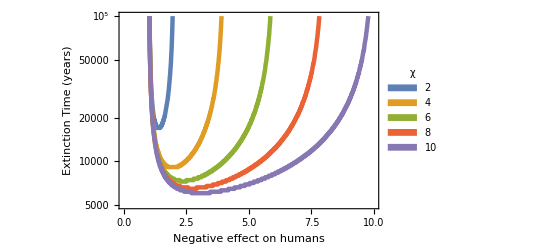

```mathematica
ExtTimePlot=
ListLogPlot[Table[PET[[All,i]],{i,1,5}],PlotRange->{5000,10^5},PlotStyle->Thickness[.008],Frame->True,FrameLabel->{"Negative effect on humans","Extinction Time (years)"},Joined->True,PlotLegends->SwatchLegend[Automatic,cvalues,LegendLabel->"χ"]]
```

```mathematica
Export["/Users/justinyeakel/Dropbox/PostDoc/2016_Frankenstein/fig_ExtTime.pdf",ExtTimePlot,"PDF"]
```

/Users/justinyeakel/Dropbox/PostDoc/2016_Frankenstein/fig_ExtTime.pdf

```mathematica
Remove[t]
```

Can we calculate the extinction time as a function of amh and ahm assuming that kh, km, rm, rh are set?

```mathematica
Table[PET[[All,i]],{i,1,6}]
```

Part::partw: Part 6 of {{0.01, ∞}, {0.01, ∞}, {0.01, ∞}, {0.01, ∞}, {0.01, ∞}} does not exist.

{{{0.01,∞},{0.01,∞},{0.01,∞},{0.01,∞},{0.01,∞}},{{0.015,∞},{0.015,∞},{0.015,∞},{0.015,∞},{0.015,∞}},{{0.02,∞},{0.02,∞},{0.02,∞},{0.02,∞},{0.02,∞}},1993,{{9.99,∞},{9.99,∞},{9.99,∞},{9.99,∞},{9.99,1.77828×10^6}},{{9.995,∞},{9.995,∞},{9.995,∞},{9.995,∞},{9.995,3.54813×10^6}},{{10.,∞},{10.,∞},{10.,∞},{10.,∞},{10.,∞}}}⟦All,6⟧
 |  |  |  |

```mathematica
tExt=Import["/Users/justinyeakel/Dropbox/PostDoc/2016_Frankenstein/d_text.csv","table"];
tExtAM=Import["/Users/justinyeakel/Dropbox/PostDoc/2016_Frankenstein/d_textam.csv","table"];
```

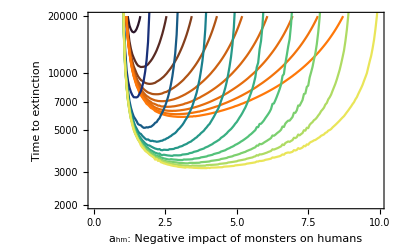

```mathematica
PAll = Show[{ColorData["RustTones","Image"]},AspectRatio->1];
PAM=Show[{ColorData["BlueGreenYellow","Image"]},AspectRatio->1];
PlotAMExt=Show[{
ListLogPlot[Table[Transpose[{Table[j,{j,1,10,0.05}],tExt[[All,i]]}],{i,1,Length[tExt[[1,All]]]}],Joined->True,PlotStyle->"RustTones",PlotRange->{2000,2*10^4},Frame->True,FrameLabel->{"a_hm: Negative impact of monsters on humans","Time to extinction"},
PlotLegends->Placed[SwatchLegend[{"Global","Amazon catalyst"},LegendMarkers->{PAll,PAM}],{ 0.8,0.15}]],
ListLogPlot[Table[Transpose[{Table[j,{j,1,10,0.05}],tExtAM[[All,i]]}],{i,1,Length[tExt[[1,All]]]}],Joined->True,PlotStyle->"BlueGreenYellow"]
}]
```

```mathematica
Export["/Users/justinyeakel/Dropbox/PostDoc/2016_Frankenstein/fig_AmExt.pdf",PlotAMExt,"PDF"]
```

/Users/justinyeakel/Dropbox/PostDoc/2016_Frankenstein/fig_AmExt.pdf

```mathematica
ColorData["BlueGreenYellow"]
```

ColorDataFunction[…]